# Tarea 4

Estudiante: José Alfredo de León

Nota: en el repositorio se encuentran disponibles los datos que se calcularon en este Notebook. Para más información de cómo extraerla o dudas comunicarse a deleongarrido.jose@gmai.com

Todo se encuentra en el repositorio: https://github.com/deleonja/mscsc_2022-2

## Definición de rutinas

```mathematica
(* Assignationk[M,N,n] computes the value of k for the Fock state n of N bosons and M sites *)
Assignationk[M_,N_,n_]:=If[n[[1;;M-1]]==ConstantArray[0,M-1],M-1,FromDigits[Last[Position[Normal[n[[1;;M-1]]],x_ /;x!=0]]]]

(* HilbertSpaceDim[N, M] computes the dimension of Hilbert Space of N bosons and M sites *)
HilbertSpaceDim[N_,M_]:=((N+M-1)!)/(N!(M-1)!)

(* FockBasis[N, M] computes the basis of Fock states for N bosons and M sites *)
FockBasis[N_,M_]:=Module[{k,fockState},
k=1;
Join[
(* Compute the first lexycographical Fock state *)
{fockState=SparseArray[{1->N},{M}]},
(* Construct the following elements of Fock basis *)
Table[
(* With η the new Fock state and n the previous one, assign Subscript[η, i]=Subscript[n, i] (1<=i<=k-1), Subscript[η, k]=Subscript[n, k]-1 y Subscript[η, i]=0 (i>=k+2) *)
fockState=SparseArray[Join[Table[i->fockState[[i]],{i,k-1}],{k->fockState[[k]]-1}],{M}];
(* With η the new Fock state and n the previous one, assign Subscript[η, k+1]=N-∑_(i=1)^k Subscript[η, i] *)
fockState[[k+1]]=N-Total[fockState[[1;;k]]];
(* Compute next value of k *)
k=Assignationk[M,N,fockState];
fockState
,HilbertSpaceDim[N,M]-1]
]
]

(*Computes the tag FockBasisElement following Tag[FockBasisElement]=∑_(i=1)^M √(100i+3)FockBasisElement[i]*)
Tag[FockBasisElement_]:=N[Round[Sum[Sqrt[100 i+3]#[[i+1]],{i,0,Length[#]-1}]&[FockBasisElement],10^-8]]
Tag[Nothing]:=Nothing

(* a[i_,fockState_] implements the action of anihiliation operator acting over fockState, with fockState of the form {Subscript[c, i],Subscript[v, i]}, with Subscript[c, i] the constant of vector Subscript[v, i] *)
a[i_,fockState_]:=If[#[[2,i]]==0,{0,Nothing},{#[[1]] Sqrt[#[[2,i]]],ReplacePart[#[[2]],i->#[[2,i]]-1]}]&[fockState]
a[i_,{0,Nothing}]:={0,Nothing}

(* a[i_,fockState_] implements the action of creation operator acting over fockState, with fockState of the form {Subscript[c, i],Subscript[v, i]}, with Subscript[c, i] the constant of vector Subscript[v, i] *)
a†[i_,fockState_,N_]:=If[#[[2,i]]==N,{0,Nothing},{#[[1]] Sqrt[#[[2,i]]+1],ReplacePart[#[[2]],i->#[[2,i]]+1]}]&[fockState]
a†[i_,{0,Nothing},N_]:={0,Nothing}

(*SearchTagPosition[tagv_,sortedTags_] searches for the position of tagv in array sortedTags. *)
SearchTagPosition[tagv_,sortedTags_]:=FromDigits[Flatten[Position[sortedTags,tagv]]]

(*NearestNeighborIndices[M_] computes the set of indices of nearest neighbours of M sites.*)
NearestNeighborIndices[M_]:=Transpose[Join[{#},{RotateLeft[#]}]]&[Range[M]]

(*ortFockBasis[fockBasis_] sorts Fock basis according to its tags.*)
SortFockBasis[fockBasis_]:=Transpose[Sort[{Tag[#],#}&/@fockBasis]]

(*Hkin[sortedBasis_,sortedTags_] computes the kinetic term T of Bose hubbard model.*)
Hkin[sortedBasis_,sortedTags_]:=Module[{HKin,d,k,i,j,tagu,l,n,M,u},
d=Length[sortedBasis];n=Plus@@sortedBasis[[1]];M=Length[sortedBasis[[1]]];
HKin=SparseArray[ConstantArray[0,{d,d}]];
k=1;
Do[
Do[
i=ij[[1]];j=ij[[2]];
u=a†[i,a[j,{1,v}],n];
If[u[[1]]==0,Continue,tagu=Tag[u[[2]]];
l=SearchTagPosition[tagu,sortedTags];
HKin+=SparseArray[{k,l}->N[u[[1]]],{d,d}]];,
{ij,NearestNeighborIndices[M]}];
k=k+1;,
{v,sortedBasis}];HKin+ConjugateTranspose[HKin]]

(*Hint[sortedBasis_] computes the interaction term T of Bose hubbard model.*)
Hint[sortedBasis_]:=Module[{d},d=Length[sortedBasis];
SparseArray[Table[{i,i},{i,d}]->Table[N[ Plus@@(#^2-#&/@v)],{v,sortedBasis}],{d,d}]]

(*BoseHubbardH[n_Integer,M_Integer,t_Real,U_Real] computes the Bose-Hubbard Hamiltonian of n particles, M sites with hopping parameter t and interaction parameter U.*)
BoseHubbardH[n_Integer,M_Integer,t_Real,U_Real]:=Module[{sortedBasis,sortedTags},
{sortedTags,sortedBasis}=SortFockBasis[FockBasis[n,M]];
-t Hkin[sortedBasis,sortedTags]+U/2Hint[sortedBasis]]

(*BoseHubbardH[n_Integer,M_Integer,t_Real,U_Real] computes the Bose-Hubbard Hamiltonian of n particles, M sites with hopping parameter t and interaction parameter U given the arrays for T and U terms.*)
BoseHubbardH[t_Real,U_Real,Hkin_,Hint_]:=-t Hkin+U/2 Hint

(*Subroutine to compute the ground state of a given Hamiltonian H.*)
GroundStateEnergy[H_]:=FromDigits[Chop[-Eigenvalues[-H,1,Method->{"Arnoldi","MaxIterations"->10^5,"Criteria"->"RealPart"}]]]

(*GroundState[H_] computes the ground state of H.*)
GroundState[H_]:=
Normalize@Chop[Flatten[Eigenvectors[H-Norm[Flatten[H]]IdentityMatrix[Dimensions[H]],1],1]]

(*Subroutine to compute the Ground State Energy of Bose-Hubbard Hamiltonian.*)
GSEBoseHubbard[N_,M_,t_,U_]:=Module[{H,sortedTags,sortedBasis},
{sortedTags,sortedBasis}=SortFockBasis[FockBasis[N,M]];
H=BoseHubbardH[sortedBasis,sortedTags,t,U];
GroundStateEnergy[H]]

(*Subroutine to compute the chemical potential*)
SuperPlus[μ][H1_,H2_]:=Chop[GroundStateEnergy[H1]-GroundStateEnergy[H2]]

(*InnerProductFockStates[v_,u_] computes the inner product of two Fock states v an u, with both lists {Subscript[c, i],Subscript[v, i]}, with Subscript[c, i] the constant multiplying the Fock ket Subscript[v, i].*)
InnerProductFockStates[v_,u_]:=If[u[[2]]==v[[2]],u[[1]]v[[1]],0]

(*SPDM[groundState_,Ν_,M_]* computes the SPDM given a groundState of N particles and M sites.*)
SPDM[groundState_,Ν_,M_]:=Module[{ϕ,vecs,d},
d=HilbertSpaceDim[Ν,M];
Table[
ϕ=Select[Normal@a†[k,a[l,#],Ν]&/@groundState,#[[1]]!=0&];
Plus@@Flatten[Table[InnerProductFockStates[groundState[[j]],ϕ[[i]]],{i,Length[ϕ]},{j,Length[groundState]}]]
,{k,M},{l,M}]]

(*Subroutine to compute the largest eigenvalue of a given matrix M.*)
LargestEigv[M_]:=FromDigits[Eigenvalues[M,1,Method->{"Arnoldi","MaxIterations"->10^5,"Criteria"->"RealPart"}]]
```

## Probando algunas de las rutinas nuevas

### Tagging Fock basis of N=4, M=4

```mathematica
Tag[#]&/@FockBasis[4,4]
```

{40.596,44.694,47.854,50.522,48.793,51.952,54.62,55.112,57.78,60.448,52.892,56.051,58.719,59.21,61.878,64.546,62.37,65.038,67.706,70.373,56.991,60.15,62.818,63.309,65.977,68.645,66.468,69.136,71.804,74.472,69.628,72.296,74.964,77.631,80.299}

## Calculando las cantidades de interés

### Factor de condensado

#### t/U

```mathematica
data=Table[
{sortedTags,sortedBasis}=SortFockBasis[FockBasis[j,j]];
Hkin1=Hkin[sortedBasis,sortedTags];
Hint1=Hint[sortedBasis];
Table[
H=BoseHubbardH[N[i],1.,Hkin1,Hint1];
groundState=Transpose[{GroundState[H],sortedBasis}];
ρ=SPDM[groundState,j,j];
λ=LargestEigv[ρ];
{i,λ/N[j]},{i,0,1,0.02}],
{j,3,6}];
```

$Aborted

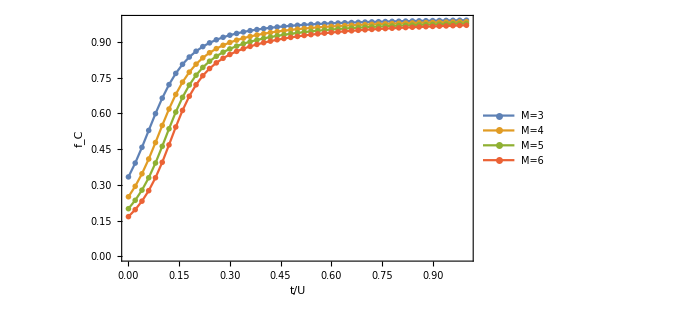

```mathematica
fig=ListPlot[data,Joined->True,PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,PlotLegends->{"M=3","M=4","M=5","M=6","M=7"},LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"t/U","f_C"}]
```

#### U/t

```mathematica
data=Table[
{sortedTags,sortedBasis}=SortFockBasis[FockBasis[j,j]];
Hkin1=Hkin[sortedBasis,sortedTags];
Hint1=Hint[sortedBasis];
Table[
H=BoseHubbardH[1.,N[i],Hkin1,Hint1];
groundState=Transpose[{GroundState[H],sortedBasis}];
ρ=SPDM[groundState,j,j];
λ=LargestEigv[ρ];
{i,λ/N[j]},{i,0,20,0.4}],
{j,3,6}];
```

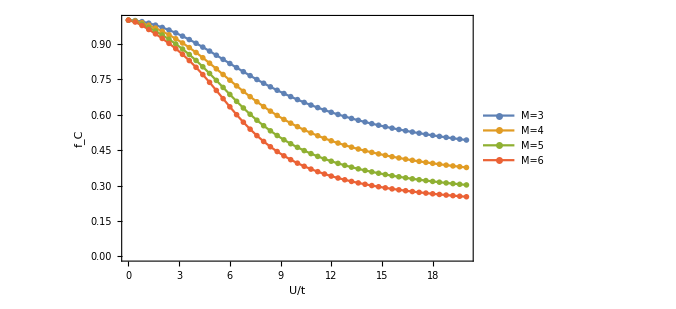

```mathematica
fig=ListPlot[data,Joined->True,PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,PlotLegends->{"M=3","M=4","M=5","M=6","M=7"},LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"U/t","f_C"}]
```

### Potenciales químicos

#### t/U

```mathematica
data=Table[
{sortedTags1,sortedBasis1}=SortFockBasis[FockBasis[j+1,j]];
{sortedTags2,sortedBasis2}=SortFockBasis[FockBasis[j,j]];
Hkin1=Hkin[sortedBasis1,sortedTags1];
Hkin2=Hkin[sortedBasis2,sortedTags2];
Hint1=Hint[sortedBasis1];
Hint2=Hint[sortedBasis2];
Table[
H1=BoseHubbardH[N[i],1.,Hkin1,Hint1];
H2=BoseHubbardH[N[i],1.,Hkin2,Hint2];
{i,SuperPlus[μ][H1,H2]},{i,0,0.5,0.02}],
{j,3,8}];ExportDataSetsHW04["data_muPlus_t_u",data]
```

/home/jadeleon/Documents/2022-2/mscsc_2022-2/codigos_tareas/data_tarea04/data_muPlus_t_u.mx

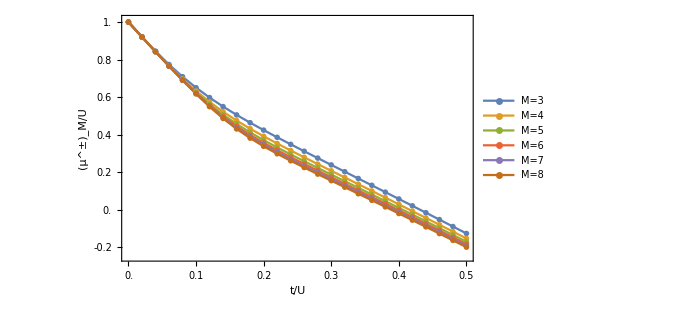

```mathematica
fig=ListPlot[data,Joined->True,PlotRange->{{0,0.5},{-0.25,1.01}},PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,PlotLegends->{"M=3","M=4","M=5","M=6","M=7","M=8"},AxesLabel->{"t/U","(μ^±)_M/U"},LabelStyle->Directive[Black,FontSize->15],FrameLabel->{"t/U","(μ^±)_M/U"},FrameTicks->{{Table[i,{i,-0.2,1,0.2}],None},{Table[i,{i,0,0.5,0.1}],None}}]
```

```mathematica
data=Table[
{sortedTags1,sortedBasis1}=SortFockBasis[FockBasis[j,j]];
{sortedTags2,sortedBasis2}=SortFockBasis[FockBasis[j-1,j]];
Hkin1=Hkin[sortedBasis1,sortedTags1];
Hkin2=Hkin[sortedBasis2,sortedTags2];
Hint1=Hint[sortedBasis1];
Hint2=Hint[sortedBasis2];
Table[
H1=BoseHubbardH[N[i],1.,Hkin1,Hint1];
H2=BoseHubbardH[N[i],1.,Hkin2,Hint2];
{i,SuperPlus[μ][H1,H2]},{i,0,0.5,0.02}],
{j,3,8}];ExportDataSetsHW04["data_muMinus_t_u",data];
```

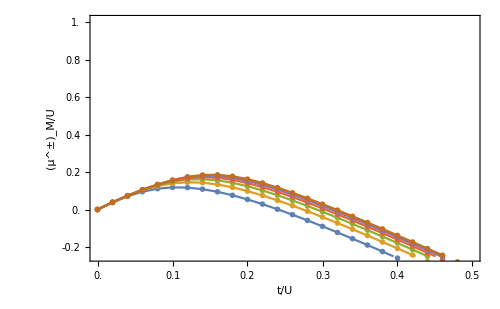

```mathematica
fig2=ListPlot[data,Joined->True,PlotRange->{{0,0.5},{-0.25,1.01}},PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,AxesLabel->{"t/U","(μ^±)_M/U"},LabelStyle->Directive[Black,FontSize->15],FrameLabel->{"t/U","(μ^±)_M/U"},FrameTicks->{{Table[i,{i,-0.2,1,0.2}],None},{Table[i,{i,0,0.5,0.1}],None}}]
```

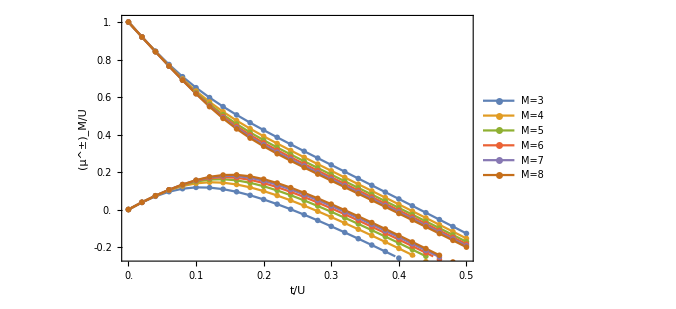

```mathematica
fig3=Show[fig,fig2]
```

#### U/t

```mathematica
data=Table[
{sortedTags1,sortedBasis1}=SortFockBasis[FockBasis[j+1,j]];
{sortedTags2,sortedBasis2}=SortFockBasis[FockBasis[j,j]];
Hkin1=Hkin[sortedBasis1,sortedTags1];
Hkin2=Hkin[sortedBasis2,sortedTags2];
Hint1=Hint[sortedBasis1];
Hint2=Hint[sortedBasis2];
Table[
H1=BoseHubbardH[1.,N[i],Hkin1,Hint1];
H2=BoseHubbardH[1.,N[i],Hkin2,Hint2];
{i,SuperPlus[μ][H1,H2]},{i,0,20,0.4}],
{j,3,8}];ExportDataSetsHW04["data_muPlus_u_t",data]
```

/home/jadeleon/Documents/2022-2/mscsc_2022-2/codigos_tareas/data_tarea04/data_muPlus_u_t.mx

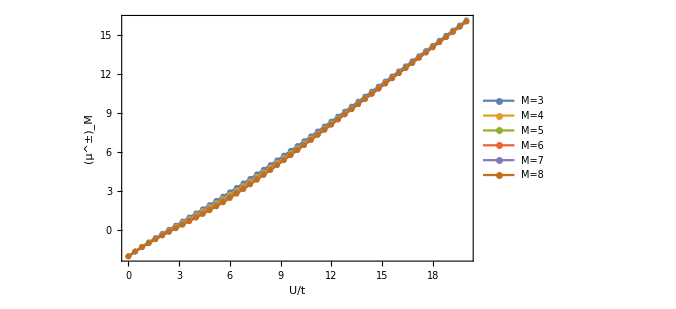

```mathematica
fig1=ListPlot[data,Joined->True,PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,PlotLegends->{"M=3","M=4","M=5","M=6","M=7","M=8"},LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"U/t","(μ^±)_M"},FrameTicks->{{All,All},{All,None}}]
```

```mathematica
data=Table[
{sortedTags1,sortedBasis1}=SortFockBasis[FockBasis[j,j]];
{sortedTags2,sortedBasis2}=SortFockBasis[FockBasis[j-1,j]];
Hkin1=Hkin[sortedBasis1,sortedTags1];
Hkin2=Hkin[sortedBasis2,sortedTags2];
Hint1=Hint[sortedBasis1];
Hint2=Hint[sortedBasis2];
Table[
H1=BoseHubbardH[1.,N[i],Hkin1,Hint1];
H2=BoseHubbardH[1.,N[i],Hkin2,Hint2];
{i,SuperPlus[μ][H1,H2]},{i,0,20,0.4}],
{j,3,8}];ExportDataSetsHW04["data_muMinus_u_t",data]
```

/home/jadeleon/Documents/2022-2/mscsc_2022-2/codigos_tareas/data_tarea04/data_muMinus_u_t.mx

```mathematica
fig2=ListPlot[data,Joined->True,PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"U/t","(μ^±)_M"},FrameTicks->{{All,All},{All,None}}];
```

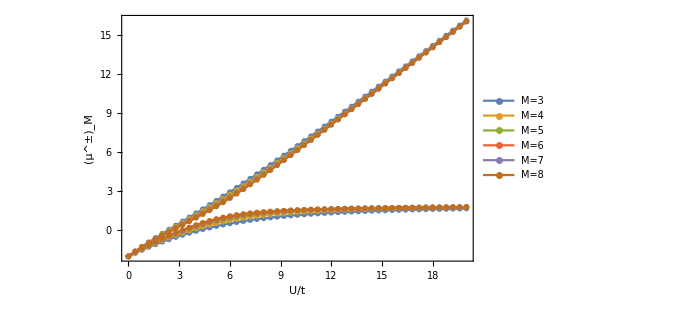

```mathematica
fig=Show[fig1,fig2]
```

### Gap de energía

Para esta cantidad se utilizaron los datos calculados en la sección anterior para los potenciales químicos.

#### t/U

```mathematica
muPlusData=Import["/home/jadeleon/Documents/2022-2/mscsc_2022-2/codigos_tareas/data_tarea04/data_muPlus_t_u.mx"];
```

```mathematica
muMinusData=Import["/home/jadeleon/Documents/2022-2/mscsc_2022-2/codigos_tareas/data_tarea04/data_muMinus_t_u.mx"];
```

```mathematica
data=muPlusData-muMinusData+Table[Table[{i,0},{i,0,0.5,0.02}],6];
```

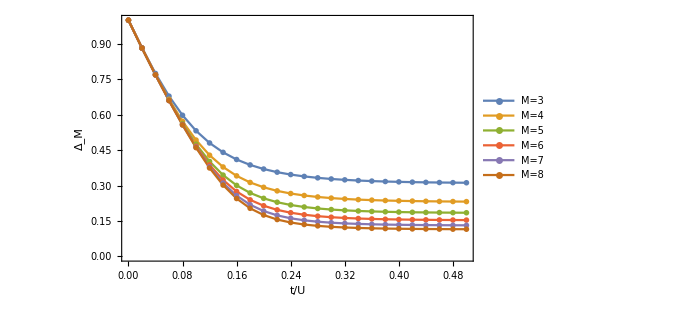

```mathematica
fig=ListPlot[data,Joined->True,PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,PlotLegends->{"M=3","M=4","M=5","M=6","M=7","M=8"},LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"t/U","Δ_M"},FrameTicks->{{All,All},{All,None}}]
```

#### U/t

```mathematica
muPlusData=Import["/home/jadeleon/Documents/2022-2/mscsc_2022-2/codigos_tareas/data_tarea04/data_muPlus_u_t.mx"];
```

```mathematica
muMinusData=Import["/home/jadeleon/Documents/2022-2/mscsc_2022-2/codigos_tareas/data_tarea04/data_muMinus_u_t.mx"];
```

```mathematica
data=muPlusData-muMinusData+Table[Table[{i,0},{i,0,20,0.4}],6];
ExportDataSetsHW04["data_energy_gap_u_t",data];
```

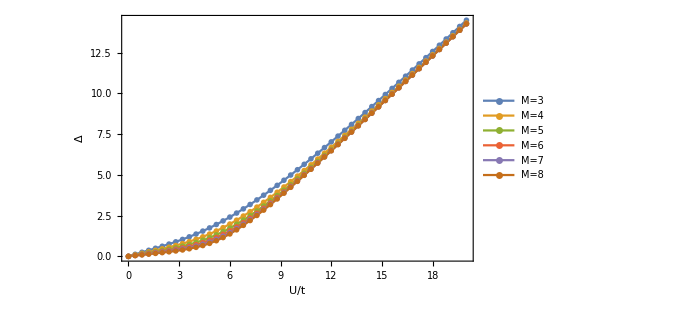

```mathematica
fig=ListPlot[data,Joined->True,PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,PlotLegends->{"M=3","M=4","M=5","M=6","M=7","M=8"},LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"U/t","Δ"},FrameTicks->{{All,All},{All,None}}]
```

### Energía cinética

#### t/U

```mathematica
data=Table[
{sortedTags,sortedBasis}=SortFockBasis[FockBasis[j,j]];
Hkin1=Hkin[sortedBasis,sortedTags];
Hint1=Hint[sortedBasis];
Table[
H=BoseHubbardH[N[i],1.,Hkin1,Hint1];
groundState=Transpose[{GroundState[H],sortedBasis}];
E0=GroundStateEnergy[H];
{i,ExpValT[groundState,E0,1.]},{i,0,1,0.02}],
{j,3,7}];
ExportDataSetsHW04["data_K_energy_t_u",data]
```

/home/jadeleon/Documents/2022-2/mscsc_2022-2/codigos_tareas/data_tarea04/data_K_energy_t_u.mx

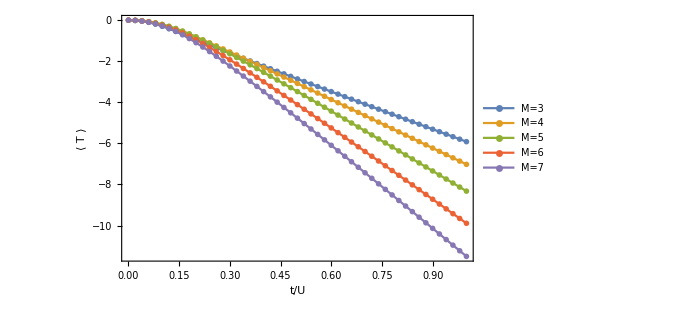

```mathematica
fig=ListPlot[data,Joined->True,PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,PlotLegends->{"M=3","M=4","M=5","M=6","M=7"},LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"t/U","⟨ T ⟩"},FrameTicks->{{All,All},{All,None}}]
```

#### U/t

```mathematica
data=Table[
{sortedTags,sortedBasis}=SortFockBasis[FockBasis[j,j]];
Hkin1=Hkin[sortedBasis,sortedTags];
Hint1=Hint[sortedBasis];
Table[
H=BoseHubbardH[1.,N[i],Hkin1,Hint1];
groundState=Transpose[{GroundState[H],sortedBasis}];
E0=GroundStateEnergy[H];
{i,ExpValT[groundState,E0,1.]},{i,0,20,0.4}],
{j,3,7}];
ExportDataSetsHW04["data_K_energy_u_t",data]
```

/home/jadeleon/Documents/2022-2/mscsc_2022-2/codigos_tareas/data_tarea04/data_K_energy_u_t.mx

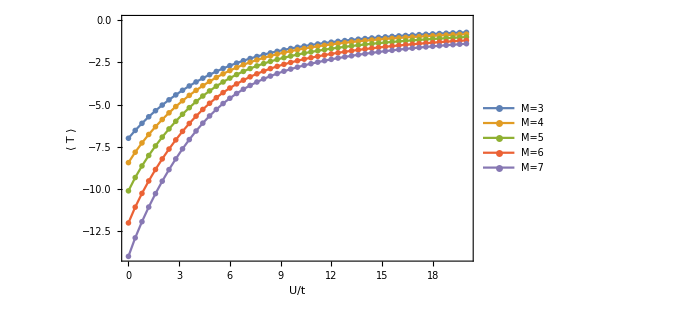

```mathematica
fig=ListPlot[data,Joined->True,PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,PlotLegends->{"M=3","M=4","M=5","M=6","M=7"},LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"U/t","⟨ T ⟩"},FrameTicks->{{All,All},{All,None}}]
```

### Fluctuaciones

#### t/U

```mathematica
data=Table[
{sortedTags,sortedBasis}=SortFockBasis[FockBasis[j,j]];
Hkin1=Hkin[sortedBasis,sortedTags];
Hint1=Hint[sortedBasis];
Table[
H=BoseHubbardH[N[i],1.,Hkin1,Hint1];
(*En este caso necesito sólo las constantes*)
groundState=GroundState[H];
{i,FluctuationsNumberOperator[groundState,j,sortedBasis]},{i,0,1,0.02}],
{j,3,7}];
```

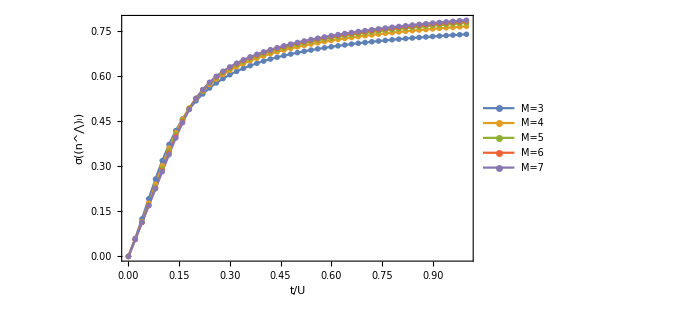

```mathematica
fig=ListPlot[data,Joined->True,PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,PlotLegends->{"M=3","M=4","M=5","M=6","M=7"},LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"t/U","σ((n^⋀)_i)"},FrameTicks->{{All,All},{All,None}}]
```

#### U/t

```mathematica
data1=Table[
{sortedTags,sortedBasis}=SortFockBasis[FockBasis[j,j]];
Hkin1=Hkin[sortedBasis,sortedTags];
Hint1=Hint[sortedBasis];
Table[
H=BoseHubbardH[1.,N[i],Hkin1,Hint1];
(*En este caso necesito sólo las constantes*)
groundState=GroundState[H];
{i,FluctuationsNumberOperator[groundState,j,sortedBasis]},{i,0,20,0.5}],
{j,7,7}];
```

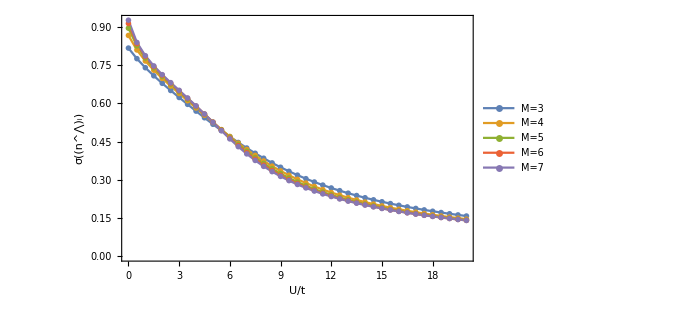

```mathematica
fig=ListPlot[data,Joined->True,PlotMarkers->{"OpenMarkers",5},Frame->True,ImageSize->500,PlotLegends->{"M=3","M=4","M=5","M=6","M=7"},LabelStyle->Directive[Black,FontSize->18],FrameLabel->{"U/t","σ((n^⋀)_i)"},FrameTicks->{{All,All},{All,None}}]
```